# Large self-coupling approximation

## Solution

### Equations

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<NumericalCalculus`
```

```mathematica
x={t,r,θ,ϕ};
gtt=-Exp[ν[r]];
grr=Exp[u[r]];
gθθ=r^2;
gϕϕ=r^2*Sin[θ]^2;
g=DiagonalMatrix[{gtt,grr,gθθ,gϕϕ}];
ginv=Inverse[g];
dim=Length[g];
Γ=Table[1/2Sum[ginv[[a,d]](D[g[[d,c]],x[[b]]]+D[g[[b,d]],x[[c]]]-D[g[[b,c]],x[[d]]]),{d,1,dim}],{a,1,dim},{b,1,dim},{c,1,dim}];
Ricci=Table[Sum[D[Γ[[c,a,b]],x[[c]]]-D[Γ[[c,c,b]],x[[a]]]+Sum[Γ[[c,c,d]]Γ[[d,a,b]]-Γ[[c,a,d]]Γ[[d,c,b]],{d,1,dim}],{c,1,dim}],{a,1,dim},{b,1,dim}];
R=Sum[ginv[[a,b]]*Ricci[[a,b]],{a,1,dim},{b,1,dim}];
Einstein=Table[Ricci[[a,b]]-1/2g[[a,b]]*R,{a,1,dim},{b,1,dim}];
```

```mathematica
(*Tensore impulso-energia*)
Φ[x]=Φ0[r]*Exp[ⅈ*ω*t];
T=Table[D[Φ[x],x[[a]]]**D[Φ[x],x[[b]]]+D[Φ[x],x[[a]]]*D[Φ[x],x[[b]]]*-g[[a,b]](Sum[ginv[[c,d]]*D[Φ[x],x[[c]]]**D[Φ[x],x[[d]]],{c,1,dim},{d,1,dim}]+V[Abs[Φ[x]]^2]),{a,1,dim},{b,1,dim}];
```

```mathematica
(*equazioni di Einstein*)
eqn1=FullSimplify[Einstein[[1,1]]-8*Pi*T[[1,1]],{Element[x,Reals],Element[{Φ0[r],Φ0'[r],ω},Reals]}]
eqn2=FullSimplify[Einstein[[2,2]]-8*Pi*T[[2,2]],{Element[x,Reals],Element[{Φ0[r],Φ0'[r],ω},Reals]}]
```

-8 ⅇ^ν[r] π V[Φ0[r]^2]-8 π ω^2 Φ0[r]^2+(ⅇ^(-u[r]+ν[r]) (-1+ⅇ^u[r]+r (u'[r]-8 π r Φ0'[r]^2)))/r^2

8 ⅇ^u[r] π (V[Φ0[r]^2]-ⅇ^(-ν[r]) ω^2 Φ0[r]^2)+(1-ⅇ^u[r]+r ν'[r])/r^2-8 π Φ0'[r]^2

```mathematica
(*Equazione di Klein-Gordon*)
eqn3=FullSimplify[Exp[-ⅈ*ω*t](1/Sqrt[-Det[g]]Sum[D[Sqrt[-Det[g]]ginv[[a,b]]D[Φ[x],x[[b]]],x[[a]]],{a,1,dim},{b,1,dim}]-D[V[q],q]*Φ[x])/.q->Abs[Φ[x]]^2,{Element[x,Reals],Element[{Φ0[r],Φ0'[r],ω},Reals]}]
```

Φ0[r] (ⅇ^(-ν[r]) ω^2-V'[Φ0[r]^2])+(ⅇ^(-u[r]) ((4-r u'[r]+r ν'[r]) Φ0'[r]+2 r Φ0''[r]))/(2 r)

### λϕ^4 self-interactions

```mathematica
V[q_]:=m^2q+γ/3q^3;
```

### Rescaling (https://arxiv.org/abs/2203.07442)

```mathematica
eqnn1=eqn1/. {Φ0[r]->Φ0[r]*m^(1/2)/γ^(1/4),Φ0'[r]->Φ0'[r]*m^2/Sqrt[γ],Φ0''[r]->m^(7/2)/γ^(3/4)*Φ0''[r],ω->m*ω,ν'[r]->m^(3/2)/γ^(1/4)*ν'[r],ν''[r]->m^(6/2)/Sqrt[γ]*ν''[r],u'[r]->m^(3/2)/γ^(1/4)*u'[r],u''[r]->m^(6/2)/Sqrt[γ]*u''[r],r->r*γ^(1/4)/m^(3/2)};
eqnnn1=eqnn1/. {Φ0[r*γ^(1/4)/m^(3/2)]->Φ0[r],Φ0'[r*γ^(1/4)/m^(3/2)]->Φ0'[r],Φ0''[r*γ^(1/4)/m^(3/2)]->Φ0''[r],ν[r*γ^(1/4)/m^(3/2)]->ν[r],ν'[r*γ^(1/4)/m^(3/2)]->ν'[r],ν''[r*γ^(1/4)/m^(3/2)]->ν''[r],u[r*γ^(1/4)/m^(3/2)]->u[r],u'[r*γ^(1/4)/m^(3/2)]->u'[r],u''[r*γ^(1/4)/m^(3/2)]->u''[r]};
eq1=FullSimplify[eqnnn1]

eqnn2=eqn2/.  {Φ0[r]->Φ0[r]*m^(1/2)/γ^(1/4),Φ0'[r]->Φ0'[r]*m^2/Sqrt[γ],Φ0''[r]->m^(7/2)/γ^(3/4)*Φ0''[r],ω->m*ω,ν'[r]->m^(3/2)/γ^(1/4)*ν'[r],ν''[r]->m^(6/2)/Sqrt[γ]*ν''[r],u'[r]->m^(3/2)/γ^(1/4)*u'[r],u''[r]->m^(6/2)/Sqrt[γ]*u''[r],r->r*γ^(1/4)/m^(3/2)};
eqnnn2=eqnn2/. {Φ0[r*γ^(1/4)/m^(3/2)]->Φ0[r],Φ0'[r*γ^(1/4)/m^(3/2)]->Φ0'[r],Φ0''[r*γ^(1/4)/m^(3/2)]->Φ0''[r],ν[r*γ^(1/4)/m^(3/2)]->ν[r],ν'[r*γ^(1/4)/m^(3/2)]->ν'[r],ν''[r*γ^(1/4)/m^(3/2)]->ν''[r],u[r*γ^(1/4)/m^(3/2)]->u[r],u'[r*γ^(1/4)/m^(3/2)]->u'[r],u''[r*γ^(1/4)/m^(3/2)]->u''[r]};
eq2=FullSimplify[eqnnn2]

eqnn3=eqn3/.  {Φ0[r]->Φ0[r]*m^(1/2)/γ^(1/4),Φ0'[r]->Φ0'[r]*m^2/Sqrt[γ],Φ0''[r]->m^(7/2)/γ^(3/4)*Φ0''[r],ω->m*ω,ν'[r]->m^(3/2)/γ^(1/4)*ν'[r],ν''[r]->m^(6/2)/Sqrt[γ]*ν''[r],u'[r]->m^(3/2)/γ^(1/4)*u'[r],u''[r]->m^(6/2)/Sqrt[γ]*u''[r],r->r*γ^(1/4)/m^(3/2)};
eqnnn3=eqnn3/. {Φ0[r*γ^(1/4)/m^(3/2)]->Φ0[r],Φ0'[r*γ^(1/4)/m^(3/2)]->Φ0'[r],Φ0''[r*γ^(1/4)/m^(3/2)]->Φ0''[r],ν[r*γ^(1/4)/m^(3/2)]->ν[r],ν'[r*γ^(1/4)/m^(3/2)]->ν'[r],ν''[r*γ^(1/4)/m^(3/2)]->ν''[r],u[r*γ^(1/4)/m^(3/2)]->u[r],u'[r*γ^(1/4)/m^(3/2)]->u'[r],u''[r*γ^(1/4)/m^(3/2)]->u''[r]};
eq3=FullSimplify[eqnnn3]
```

(ⅇ^(-u[r]) m^3 (ⅇ^u[r] √γ (3 ⅇ^ν[r]-8 π r^2 Φ0[r]^2 (3 ω^2+ⅇ^ν[r] (3+Φ0[r]^4)))-3 ⅇ^ν[r] (√γ (1-r u'[r])+8 m π r^2 Φ0'[r]^2)))/(3 r^2 γ)

(m^3 (8 ⅇ^(u[r]-ν[r]) π √γ Φ0[r]^2 (-3 ω^2+ⅇ^ν[r] (3+Φ0[r]^4))+(3 √γ (1-ⅇ^u[r]+r ν'[r]))/r^2-24 m π Φ0'[r]^2))/(3 γ)

(m^(5/2) (-2 ⅇ^(-ν[r]) √γ (ⅇ^ν[r]-ω^2) Φ0[r]-2 √γ Φ0[r]^5+(ⅇ^(-u[r]) m ((4-r u'[r]+r ν'[r]) Φ0'[r]+2 r Φ0''[r]))/r))/(2 γ^(3/4))

### Neglecting (spatial) derivatives

```mathematica
eq1=FullSimplify[eq1/.{Φ0'[r]->0,Φ0''[r]->0}]
```

(m^3 (-24 π (ⅇ^ν[r]+ω^2) Φ0[r]^2-8 ⅇ^ν[r] π Φ0[r]^6+(3 ⅇ^(-u[r]+ν[r]) (-1+ⅇ^u[r]+r u'[r]))/r^2))/(3 √γ)

```mathematica
eq2=FullSimplify[eq2/.{Φ0'[r]->0,Φ0''[r]->0}]
```

(m^3 (8 ⅇ^(u[r]-ν[r]) π Φ0[r]^2 (-3 ω^2+ⅇ^ν[r] (3+Φ0[r]^4))+(3-3 ⅇ^u[r]+3 r ν'[r])/r^2))/(3 √γ)

```mathematica
(*Φ2[r_,ω_]:=Max[0,σ0^3/(3*Sqrt[2])-σ0^3/(6*Sqrt[2])Sqrt[7+3/2*(-Exp[-ν[ω][r]]*σ0^2*8*Pi*ω^2)]/.sol1];*)
```

```mathematica
eq3=FullSimplify[eq3/.{Φ0'[r]->0,Φ0''[r]->0}]
```

-(ⅇ^(-ν[r]) m^(5/2) Φ0[r] (-ω^2+ⅇ^ν[r] (1+Φ0[r]^4)))/γ^(1/4)

### Solving for the scalar field

```mathematica
Φval=Assuming[{ω>0,λ>0,m>0,ν[r]>0},Solve[eq3==0/.{Φ0[r]->Sqrt[Sqrt[Φ2[r]]]},Φ2[r]]]
```

{{Φ2[r]→0},{Φ2[r]→ⅇ^(-ν[r]) (-ⅇ^ν[r]+ω^2)}}

```mathematica
eq1in=FullSimplify[eq1/.{Φ0[r]->Sqrt[Sqrt[Φval[[2]][[1]][[2]]]]}]
```

(m^3 (-24 π (ⅇ^ν[r]+ω^2) √(-1+ⅇ^(-ν[r]) ω^2)-8 ⅇ^ν[r] π (-1+ⅇ^(-ν[r]) ω^2)^(3/2)+(3 ⅇ^(-u[r]+ν[r]) (-1+ⅇ^u[r]+r u'[r]))/r^2))/(3 √γ)

```mathematica
eq2in=FullSimplify[eq2/.{Φ0[r]->Sqrt[Sqrt[Φval[[2]][[1]][[2]]]]}]
```

(m^3 (3+ⅇ^u[r] (-3+16 ⅇ^(-ν[r]) π r^2 (ⅇ^ν[r]-ω^2) √(-1+ⅇ^(-ν[r]) ω^2))+3 r ν'[r]))/(3 r^2 √γ)

### Solving Einstein equations

```mathematica
(*sviluppi in potenze di r*)
n=4;
```

```mathematica
μ[r_]:=Sum[uu[i]r^i,{i,0,2*n+2}];
v[r_]:=Sum[vv[i]r^i,{i,0,2*n+2}];
```

```mathematica
series1=Series[eq1in/.{u[r]->μ[r],u'[r]->μ'[r],u''[r]->μ''[r],ν[r]->v[r],ν'[r]->v'[r],ν''[r]->v''[r]},{r,0,2*n+4}];
series2=Series[eq2in /.{u[r]->μ[r],u'[r]->μ'[r],u''[r]->μ''[r],ν[r]->v[r],ν'[r]->v'[r],ν''[r]->v''[r]},{r,0,2*n+4}];
```

```mathematica
uu[0]=0;
Table[uu[2i+1]=0,{i,0,n}];
Table[vv[2i+1]=0,{i,0,n}];
```

```mathematica
Table[{uu[2i+2],vv[2i+2]}=Collect[Solve[{Coefficient[series1,r,2i]==0,Coefficient[series2,r,2i]==0},{uu[2i+2],vv[2i+2]}],{vv[0]},Simplify][[1,All,2]],{i,0,n}];
```

```mathematica
vv[0]=-2.80042;  (*or -6.68023*) (*Fix to reproduce a given configuration. Here you shoud use the value after the time-shift*)
```

### For pp[0] = 1 and lamda = 1000, the mass is 0.0699008870, \omega = 0.80225 and vv[0] = -2.95235

```mathematica
ω=0.865571;  (*or 0.864473*)
```

```mathematica
m=γ=1; (*Setting these values to one is the same as simplyfing the quantity m^2/√λ. It should hold for any λ provided λ/m^2>>1 *)
```

```mathematica
prec=25;
```

```mathematica
sol1=NDSolve[{SetPrecision[eq1in,prec]==0,SetPrecision[eq2in,prec]==0,u[SetPrecision[0.00001,prec]]==SetPrecision[μ[0.00001],prec],ν[SetPrecision[0.00001,prec]]==SetPrecision[v[0.00001],prec]},{ν,u},{r,0.00001,10},WorkingPrecision->20,AccuracyGoal->15,PrecisionGoal->15,MaxSteps->Infinity]
```

{{ν→InterpolatingFunction[{{0.000010000000000000000818, 10.000000000000000000}}, <>],u→InterpolatingFunction[{{0.000010000000000000000818, 10.000000000000000000}}, <>]}}

```mathematica
{nu1,u1}={sol1[[1]][[1]][[2]],sol1[[1]][[2]][[2]]};
```

```mathematica
range=Re[FindRoot[Sqrt[Sqrt[-ⅇ^(-nu1[r]) (ⅇ^nu1[r]-ω^2)]],{r,0.1}][[1]][[2]]] (*support of the scalar field*)
```

FindRoot::nlnum: The function value {(-ⅇ^(-InterpolatingFunction[{{«2»}},{5,3,1,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«4304»}},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«4294»},{Automatic}][-0.177294+«20» ⅈ]) (-0.749213+ⅇ^(«1»[-0.177294+0.106718 ⅈ])))^(1/4)} is not a list of numbers with dimensions {1} at {r} = {-0.177294+0.106718 ⅈ}.

0.199371

```mathematica
Φsolution[r_]:=Sqrt[Sqrt[-ⅇ^(-nu1[r]) (ⅇ^nu1[r]-ω^2)]]*UnitStep[-r+range]; (*whole scalar field solution*)
```

```mathematica
comp=Import["C:\\Users\\aleja\\OneDrive\\Escritorio\\master\\roma\\new rescaling\\phisol_lamda=1000_phi_1.wdx"]; (*Import a reference configuration to compare*)
```

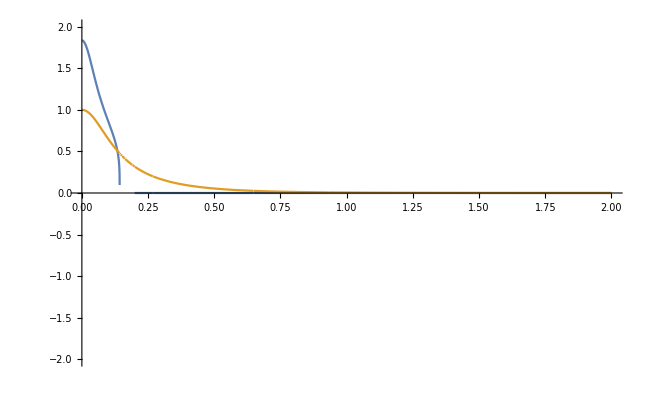

```mathematica
Plot[{Φsolution[r],comp[r]},{r,0.0001,2},PlotRange->{{0,2},{-2,2}}]
```

## Plot

```mathematica
{C1,C2,C3,C4,C5,C6,C7,C8,C9,C10,C11,C12,C13}={RGBColor["#195c92"],RGBColor["#d11141"],RGBColor["#009E60"],RGBColor["#FFA500"],
RGBColor["#34DCE3"],RGBColor["#DC00E3"],RGBColor["#8FDE44"],RGBColor["#4FB6E3"],
RGBColor["#E05BE0"],RGBColor["#1370DE"],RGBColor["#B52E66"],RGBColor["#FA6705"],RGBColor["#319F8F"]};
```

```mathematica
Integerise[x_]:=If[Round[x]==x,ToString[Round@x]<>".0",ToString@x]
```

```mathematica
xb=Join[Table[{0.5i,,{0.015,0}},{i,0,500}],Table[{2.5i,Integerise[2.5*i],{0.02,0}},{i,0,40}]];
xu=Join[Table[{0.5i,,{0.015,0}},{i,0,500}],Table[{2.5i,,{0.02,0}},{i,0,40}]];

xl=Join[Table[{0.1i,,{0.015,0}},{i,0,100}],Table[{0.5i,Integerise[0.5i],{0.025,0}},{i,1,40}]];
xr=Join[Table[{0.1i,,{0.015,0}},{i,0,100}],Table[{0.5i,,{0.025,0}},{i,1,40}]];
```

```mathematica
(*0.04 is the mass, change with the total mass of the configuration*)
```

```mathematica
rescϕsol[r_]:=Φsolution[0.0699008870*r];
```

```mathematica
rescconf[r_]:=comp[0.0699008870*r];
```

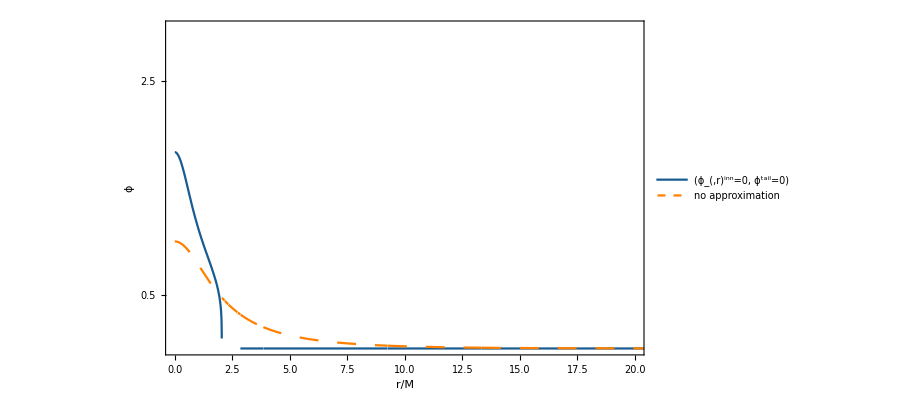

```mathematica
Plot[{rescϕsol[r],rescconf[r]},{r,0.001,25},PlotRange->{{0,20},{0,3}},Frame->True,FrameStyle->Directive[15,GrayLevel[0],FontFamily->"American Typewriter",Italic,AbsoluteThickness[1.5]],FrameLabel->{Style["r/M",18],Style["ϕ",18]},RotateLabel->False,PlotStyle->{Directive[C1,AbsoluteThickness[1.6]],Directive[Orange,Dashing[{0.02,0.02}],AbsoluteThickness[1.6]]},FrameTicks->{{xl,xr},{xb,xu}},ImagePadding->{{60,40},{50,25}},PlotLegends->Placed[{Style["(ϕ_(,r)^inn=0, ϕ^tail=0)",12,Italic,FontFamily->"American Typewriter"],Style["no approximation",12,Italic,FontFamily->"American Typewriter"]},Scaled[{0.65,0.8}]]]
```

```mathematica
Export["Fig1_lamda=1000,phi=1.png",%,ImageResolution->500]
```

Fig1_lamda=1000,phi=1.png